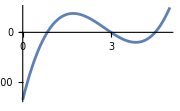

```mathematica
(* 1) *)

f[x_]:= 12 x^3-100 x^2+237x -135
Plot [f[x],{x,0,5},AxesOrigin ->{0, 0}, ImageSize->Small]
```

```mathematica
x0= 4;
x1 =5;
ϵ=10^-3;
xnew=x1-(f[x1](x1-x0))/(f[x1]-f[x0]);
i=0;

While[Abs[xnew-x1]>ϵ,x0=x1;
x1=xnew;
xnew=x1-(f[x1](x1-x0))/(f[x1]-f[x0]);
i++;]
Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 5  Корень - 4.5

```mathematica
Clear[x,f,xnew,x0,x1,i]
```

```mathematica
(* 2) *)

f=x^6+x^5-26 x^4-52 x^3+152 x^2+512x+384
```

384+512 x+152 x^2-52 x^3-26 x^4+x^5+x^6

```mathematica
Print["Корни "]
N[solutions=Solve[f==0,x],2]
N[numerical=NSolve[f==0,x],2]
Roots[f==0,x]
FindRoot[f==0,{x,1}]
Print["Разложение  ",Factor[f]]
```

Корни

{{x→-3.},{x→-2.},{x→-2.},{x→-2.},{x→4.},{x→4.}}

{{x→-3.},{x→-2.},{x→-2.},{x→-2.},{x→4.},{x→4.}}

x==-3||x==-2||x==-2||x==-2||x==4||x==4

{x→-1.99999}

Разложение  (-4+x)^2 (2+x)^3 (3+x)

```mathematica
Clear[x,f]
```

```mathematica
(* 3) *)
```

-9-2^(-4+3 x)-x+7 x^2

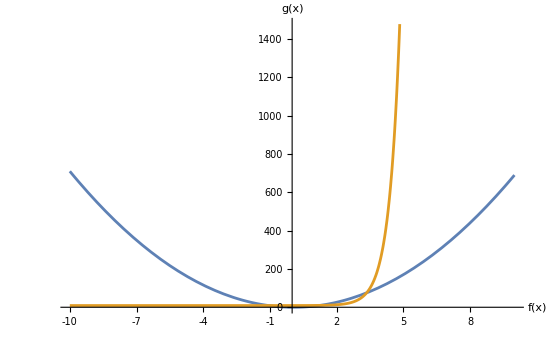

```mathematica
f[x_]:=7 x^2-x-2^(3x-4)-9
Subscript[f, 0]=7 x^2-x-2^(3x-4)-9
h[x_]:=7 x^2-x
g[x_]:=2^(3x-4)+9
Plot[{h[x],g[x]},{x,-10,10},AxesLabel->{"f(x)","g(x)"},Ticks->{Range[-10,10],Automatic}]
```

```mathematica
Print["Корень  ",N[solutions=FindRoot[Subscript[f, 0]==0,{x,-4}]]]
```

Корень  {x→-0.325081}

```mathematica
x0=-1;
maxi=100;
ϵ=10^-3;
iter=0;
x=x0;
For[i=1,i<=maxi,i++,
df:=D[f[y],y];
If[df/.y->x==0,Break[]];

xnew=y-f[y]/df/.y->x;
If[Abs[xnew-x]<ϵ, iter=i; x=xnew;Break[]];
x=xnew;
]

Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 3  Корень - -1.06514

```mathematica
x=x0;
xprev=x0-0.1;
iter=0;
For[i=1,i<=maxi,i++,df:=(f[y]-f[xprev])/(y-xprev);
If[df/.y->x==0,Break[]];
xnew=x-f[x]/df/.y->x;
If[Abs[xnew-x]<ϵ,
iter=i;
x=xnew;
Break[]];
xprev=x;
x=xnew;
]
Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 3  Корень - -1.06514

```mathematica
(*  4)  *)

x0=-1;
g[x_]:=x+0.1*f[x]
ϵ=10^-3;
maxi=100;
x=x0;
i=0;
While[i<=maxi,xnext=g[x];If[Abs[xnext-x]<ϵ,Break[],x=xnext];
i++;
]
Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 9  Корень - -1.06514

```mathematica
Clear[x,f,g,h]
```

```mathematica
(*  5)  *)
```

```mathematica
h=7 x^2-x;
g=2^(3x-4)+9;
```

```mathematica
NSolve[h==g,x_]
Solve[h==g,x_]
FindRoot[h==g,{x,-1}]
```

{}

{}

{x→-1.06514}

```mathematica
Print ["Решено с помощью FindRoot  ",FindRoot[h==g,{x,-1}]]
```

Решено с помощью FindRoot  {x→-1.06514}

```mathematica
Clear[x,f,g,h]
```

```mathematica
(*  6)  *)
```

```mathematica
f[x_,y_]=(x^2+ y^2)^2-8(x^2-y^2)-65;
g[x_,y_]=2^(x+7y)+x - 9 y^2;
```

```mathematica
gr1=ContourPlot[f[x,y]==0,{x,-7,7},{y,-7,7},Axes->True,Frame->False];
```

```mathematica
gr2=ContourPlot[g[x,y]==0,{x,-7,7},{y,-7,7},Axes->True,Frame->False];
```

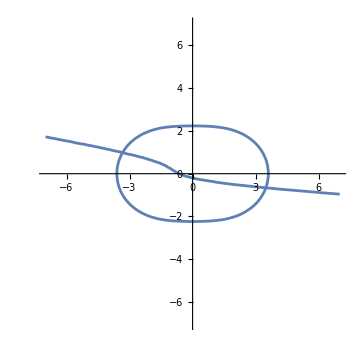

```mathematica
Show[gr1,gr2,ImageSize->Medium]
```

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-4},{y,1}]
```

{x→-3.3314,y→0.990932}

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,3},{y,0}]
```

{x→3.48773,y→-0.661668}